## Ring Wavefunction

```mathematica
DSolve[-F''[x]==k F[x],F[x],x]
```

{{F[x]→C[1] Cos[√k x]+C[2] Sin[√k x]}}

```mathematica
Subscript[ψ, k_Integer][x_]:= C[1]Cos[k x]+C[2] Sin[k x]/.{C[1]->1,C[2]->ⅈ √((-1+π)/π)}
```

```mathematica
ψ[-π]==ψ[π]
ψ'[π]==ψ'[-π]
```

Cos[k π]-C[2] Sin[k π]==Cos[k π]+C[2] Sin[k π]

k C[2] Cos[k π]-k Sin[k π]==k C[2] Cos[k π]+k Sin[k π]

```mathematica
C[2] Cos[k π]-Sin[k π]==C[2] Cos[k π]+Sin[k π]
```

C[2] Cos[k π]-Sin[k π]==C[2] Cos[k π]+Sin[k π]

```mathematica
Solve[C[2] Cos[k π]-Sin[k π]==C[2] Cos[k π]+Sin[k π],{k}]
```

{{k→ConditionalExpression[2 C[1],C[1]∈Integers]},{k→ConditionalExpression[(π+2 π C[1])/π,C[1]∈Integers]}}

```mathematica
Refine[C[2] Cos[k π]-Sin[k π]==C[2] Cos[k π]+Sin[k π],k∈Integers]
```

True

```mathematica
ParametricPlot3D[{Cos[x],Sin[x],Abs[Subscript[ψ, 20][x]]^2},{x,-π,π}]
```

-Graphics3D-

## Annulus Wave Function

### -ℏ/(2m)(∂^2/(∂r^2)+1/r∂/(∂r)+1/r^2∂^2/(∂ϕ^2))ψ[r,ϕ]==E ψ[r,ϕ]

#### r^2(R``[r])/R[r]+r (R`[r])/R[r]+r^2 λ==μ^2==-(ω``[ϕ])/ω[ϕ]

```mathematica
Subscript[ψ, λ_,μ_][r_,ϕ_]:=Subscript[R, λ,μ][r]Subscript[ω, μ][ϕ]
Subscript[ω, μ_][ϕ_]:=A Exp[ⅈ μ ϕ]
Subscript[R, λ_,μ_][r_]:=BesselJ[μ,r λ]+C BesselY[μ,r λ] /.C->0(* C=0 for Subscript[r, 0]=0*)
Subscript[ψ, 1,1][3,4.]
```

(-0.221624-0.256601 ⅈ) A

```mathematica
ω[ϕ]==ω[ϕ+2π]
```

A ⅇ^(ⅈ μ ϕ)==A ⅇ^(ⅈ μ (2 π+ϕ))

```mathematica
ⅇ^(ⅈ μ ϕ)==ⅇ^(ⅈ μ (2 π+ϕ))
1==ⅇ^(ⅈ μ 2π)
```

```mathematica
∴μ∈Integers
```

```mathematica
DSolve[R''[r]+1/r R'[r]+λ^2 R[r]== 1/r^2 μ^2 R[r],R[r],r]
```

{{R[r]→BesselJ[μ,r λ] C[1]+BesselY[μ,r λ] C[2]}}

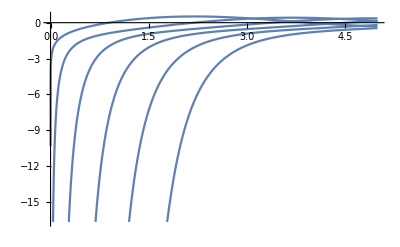

```mathematica
Plot[Table[BesselY[μ,r],{μ,0,5}],{r,0,5}]
```

```mathematica
Subscript[R, 1,0][1]
```

B BesselJ[0,1]

```mathematica
NSolve[BesselJ[3,5 λ]==0.,λ]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{λ→0.}}

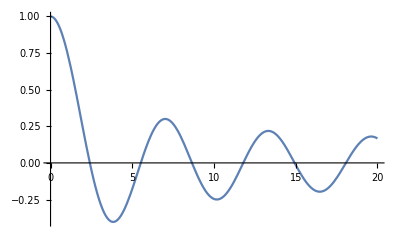

```mathematica
Plot[BesselJ[0,λ],{λ,0,20}]
```

```mathematica
Reduce[BesselJ[0,λ]==0,λ]
```

C[1]∈Integers&&C[1]≥1&&(λ==-BesselJZero[0,C[1]]||λ==BesselJZero[0,C[1]])

```mathematica
NIntegrate[BesselJ[0,r],{r,0,∞}]
```

1.

```mathematica
BesselJ[1,1]//N
```

0.440051

```mathematica
Integrate[Subscript[ψ, 1,1][r,ϕ]r,{r,0,1},{ϕ,-π,π}]
```

0

```mathematica
ParametricPlot3D[{r Cos[ϕ],r Sin[ϕ],Abs[Subscript[ψ, 1,0][r,ϕ]]^2/.{A->1}},{r,0,2},{ϕ,0,2π},PlotRange->Full]
```

-Graphics3D-

```mathematica
Re[Subscript[ψ, 1,0][1.,1.]]
```

0.765198 Re[A]

```mathematica
DSolve[{R''[r]+1/r R'[r]+λ^2 R[r]== 1/r^2 μ^2 R[r],R[1]==0},R[r],r]
```

{{R[r]→(BesselJ[μ,r λ] BesselY[μ,λ] C[1]-BesselJ[μ,λ] BesselY[μ,r λ] C[1])/BesselY[μ,λ]}}

```mathematica
Integrate[((BesselJ[μ,r λ] BesselY[μ,λ] C[1]-BesselJ[μ,λ] BesselY[μ,r λ] C[1])/BesselY[μ,λ])^2,{r,1,2}]
```

1/BesselY[μ,λ]^2 C[1]^2 (-1/(π^2 μ (-1+4 μ^2))2 λ^(-2 μ) (2 π λ^(2 μ) (-1+4 μ^2) BesselJ[μ,λ] (-BesselY[μ,λ]+BesselJ[μ,λ] Cot[π μ]) HypergeometricPFQ[{1/2,1/2},{3/2,1-μ,1+μ},-4 λ^2]+μ ((1+2 μ) BesselJ[μ,λ]^2 Gamma[μ]^2 HypergeometricPFQ[{1/2-μ,1/2-μ},{1-2 μ,1-μ,3/2-μ},-4 λ^2]-λ^(4 μ) (-1+2 μ) Gamma[-μ]^2 HypergeometricPFQ[{1/2+μ,1/2+μ},{1+μ,3/2+μ,1+2 μ},-4 λ^2] (BesselJ[μ,λ] Cos[π μ]-BesselY[μ,λ] Sin[π μ])^2))-1/(π^2 μ (-1+4 μ^2))4^-μ λ^(-2 μ) (-2^(1+2 μ) π λ^(2 μ) (-1+4 μ^2) BesselJ[μ,λ] (-BesselY[μ,λ]+BesselJ[μ,λ] Cot[π μ]) HypergeometricPFQ[{1/2,1/2},{3/2,1-μ,1+μ},-λ^2]-μ (16^μ (1+2 μ) BesselJ[μ,λ]^2 Gamma[μ]^2 HypergeometricPFQ[{1/2-μ,1/2-μ},{1-2 μ,1-μ,3/2-μ},-λ^2]-λ^(4 μ) (-1+2 μ) Gamma[-μ]^2 HypergeometricPFQ[{1/2+μ,1/2+μ},{1+μ,3/2+μ,1+2 μ},-λ^2] (BesselJ[μ,λ] Cos[π μ]-BesselY[μ,λ] Sin[π μ])^2)))